```mathematica
Quit[];
```

```mathematica
Needs["MyStyle`"]
```

### PlotStyles

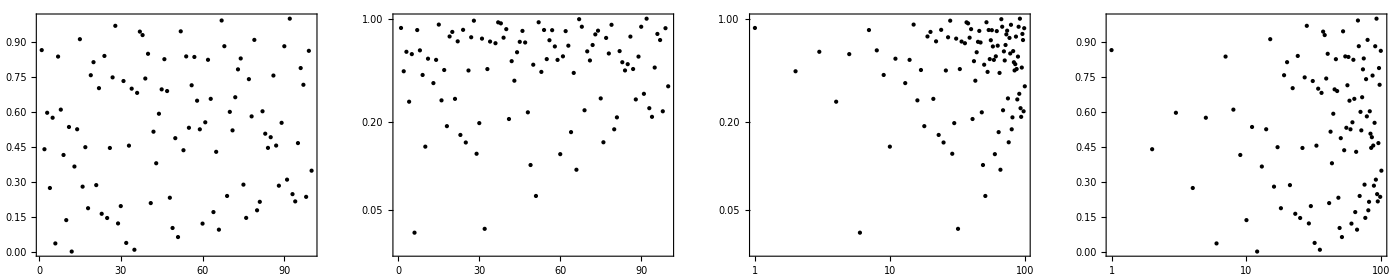

```mathematica
rndDat=RandomReal[{0,1},100];
GraphicsRow[{ListPlot[rndDat],
ListLogPlot[rndDat],
ListLogLogPlot[rndDat],
ListLogLinearPlot[rndDat]},ImageSize->4*350]
```

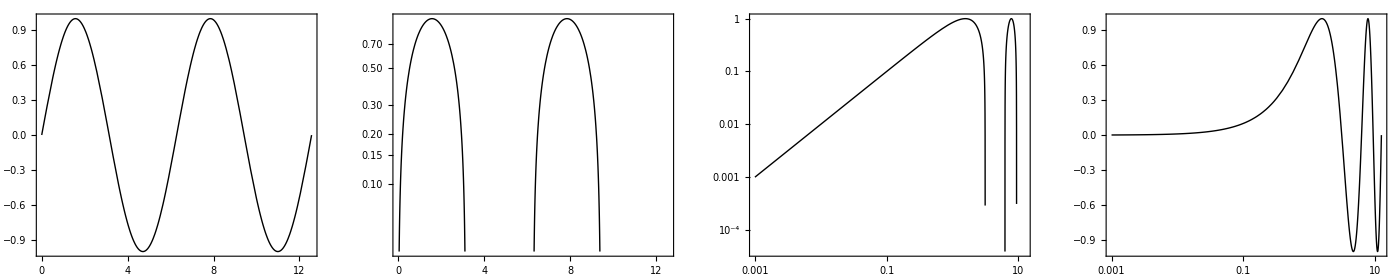

```mathematica
args=Sequence[Sin[x],{x,0.001,4Pi}];
GraphicsRow[{Plot[Evaluate[args]],
LogPlot[Evaluate[args]],
LogLogPlot[Evaluate[args]],
LogLinearPlot[Evaluate[args]]},ImageSize->4*350]
```

### errorListPlotBand

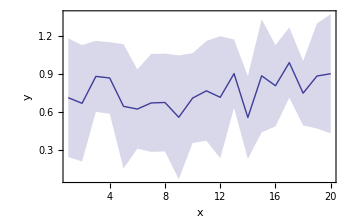

Join::heads: Heads Rule and List at positions 1 and 2 are expected to be the same.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Show::gtype: Show is not a type of graphics.

General::stop: Further output of Show :: gtype will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[GraphicsComplexBox[List[List[1.`, 0.9730454706472378`], List[2.`, 0.4769729838047392`], List[3.`, 0.33988428715526164`], List[4.`, 0.03825115005988855`], List[5.`, 0.19950141634557372`], List[6.`, 0.17581133700834406`], List[7.`, 0.08779701186799627`], List[8.`, 0.4736740580223753`], List[9.`, 0.19555121764857009`], List[10.`, 0.8109303415814553`], List[11.`, 0.6401272739435826`], List[12.`, 0.22262794575590683`], List[13.`, 0.6825814322233881`], List[14.`, 0.10478343328625095`], List[15.`, 0.6796181402737607`], List[16.`, 0.7555375385947425`], List[17.`, 0.3838672720389107`], List[18.`, 0.1346678107954764`], List[19.`, 0.7208140932450597`], List[20.`, 0.7804987414169118`], List[1.`, 1.4444844387424527`], List[2.`, 0.5231705830122785`], List[3.`, 0.546271411800345`], List[4.`, 0.21583221376866302`], List[5.`, 0.25526351884416876`], List[6.`, 0.22123011256267722`], List[7.`, 0.2695807625935138`], List[8.`, 0.7246165163532221`], List[9.`, 0.6334012742200771`], List[10.`, 1.2359790137973934`], List[11.`, 0.8904935556947028`], List[12.`, 0.34329076126634317`], List[13.`, 0.8936673645276894`], List[14.`, 0.26117928477432184`], List[15.`, 1.1752522900724407`], List[16.`, 0.982632151085133`], List[17.`, 0.8711568579237734`], List[18.`, 0.34392886113568366`], List[19.`, 1.0655120783900127`], List[20.`, 0.782815893851776`], List[1.`, 0.5016065025520229`], List[2.`, 0.4307753845971999`], List[3.`, 0.1334971625101783`], List[4.`, -0.13932991364888592`], List[5.`, 0.1437393138469787`], List[6.`, 0.1303925614540109`], List[7.`, -0.09398673885752129`], List[8.`, 0.22273159969152845`], List[9.`, -0.2422988389229369`], List[10.`, 0.38588166936551715`], Skeleton[10]], List[List[List[], List[], List[], List[], List[], List[], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[], List[], List[], List[]], List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], RGBColor[0.24720000000000014`, 0.24`, 0.6`], LineBox[List[Skeleton[20]]]], List[], List[]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[AxesOrigin, List[0, 0]], Rule[BaseStyle, List[Rule[.

Join::heads: Heads Rule and List at positions 1 and 2 are expected to be the same.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Show::gtype: Show is not a type of graphics.

General::stop: Further output of Show :: gtype will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[GraphicsComplexBox[List[List[1.`, 0.1225226994423747`], List[2.`, 0.9721430386166203`], List[3.`, 0.7660664704545446`], List[4.`, 0.7682622714169676`], List[5.`, 0.13073977846964824`], List[6.`, 0.8542595525924972`], List[7.`, 0.408832572064884`], List[8.`, 0.20452787779107462`], List[9.`, 0.7101450485962844`], List[10.`, 0.7276963056655936`], List[11.`, 0.8107083958745449`], List[12.`, 0.30003196742202287`], List[13.`, 0.6328633463709439`], List[14.`, 0.451326969226717`], List[15.`, 0.6828642262701246`], List[16.`, 0.16561587037744951`], List[17.`, 0.659187744140739`], List[18.`, 0.8003826467817714`], List[19.`, 0.38819499976472094`], List[20.`, 0.1461858158035212`], List[1.`, 0.15658109925813046`], List[2.`, 1.2821615305606686`], List[3.`, 1.0649018869787605`], List[4.`, 1.1014155299160282`], List[5.`, 0.4627937741610655`], List[6.`, 0.9114805846573137`], List[7.`, 0.6728963191553765`], List[8.`, 0.4925923346355785`], List[9.`, 1.113786166805865`], List[10.`, 1.1493188088920943`], List[11.`, 0.8617006656000391`], List[12.`, 0.5874672410826747`], List[13.`, 0.9351805200647256`], List[14.`, 0.8901702563651112`], List[15.`, 0.7336315183222211`], List[16.`, 0.4393138706959574`], List[17.`, 0.824491428310459`], List[18.`, 0.9357822188366686`], List[19.`, 0.6254298393617106`], List[20.`, 0.40607666978967083`], List[1.`, 0.08846429962661895`], List[2.`, 0.6621245466725721`], List[3.`, 0.4672310539303286`], List[4.`, 0.43510901291790705`], List[5.`, -0.201314217221769`], List[6.`, 0.7970385205276806`], List[7.`, 0.14476882497439147`], List[8.`, -0.08353657905342926`], List[9.`, 0.30650393038670365`], List[10.`, 0.306073802439093`], Skeleton[10]], List[List[List[], List[], List[], List[], List[], List[], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[], List[], List[], List[]], List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], RGBColor[0.24720000000000014`, 0.24`, 0.6`], LineBox[List[Skeleton[20]]]], List[], List[]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[AxesOrigin, List[0, 0]], Rule[BaseStyle, List[Rule[.

Join::heads: Heads Rule and List at positions 1 and 2 are expected to be the same.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Show::gtype: Show is not a type of graphics.

General::stop: Further output of Show :: gtype will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[GraphicsComplexBox[List[List[1.`, 0.5173293606530303`], List[2.`, 0.3842900342376041`], List[3.`, 0.07989286184102551`], List[4.`, 0.09139783685455605`], List[5.`, 0.2100362961082778`], List[6.`, 0.9058126572964742`], List[7.`, 0.04715113902297441`], List[8.`, 0.9331251647342009`], List[9.`, 0.038613251135762416`], List[10.`, 0.39663172134824043`], List[11.`, 0.9273607820205989`], List[12.`, 0.8454546539432075`], List[13.`, 0.9769822542949318`], List[14.`, 0.9264608431176224`], List[15.`, 0.23787869283174867`], List[16.`, 0.24360596326602013`], List[17.`, 0.8040977374531524`], List[18.`, 0.1700338701221078`], List[19.`, 0.3913316230972925`], List[20.`, 0.4185118760892246`], List[1.`, 0.753328846916316`], List[2.`, 0.40126880884562477`], List[3.`, 0.10647842296253174`], List[4.`, 0.16521053855362322`], List[5.`, 0.3274388129124507`], List[6.`, 1.2702819854060843`], List[7.`, 0.5308536336083274`], List[8.`, 1.3197191267579078`], List[9.`, 0.42508300313811276`], List[10.`, 0.706420035756801`], List[11.`, 1.2162917926314802`], List[12.`, 1.1964674323073785`], List[13.`, 1.0099337665550085`], List[14.`, 1.1876430263339413`], List[15.`, 0.5514686097084263`], List[16.`, 0.5835615010290447`], List[17.`, 1.2992820385654196`], List[18.`, 0.39439581497502263`], List[19.`, 0.52229620065696`], List[20.`, 0.826894737466795`], List[1.`, 0.28132987438974455`], List[2.`, 0.36731125962958344`], List[3.`, 0.05330730071951928`], List[4.`, 0.017585135155488874`], List[5.`, 0.09263377930410488`], List[6.`, 0.5413433291868641`], List[7.`, -0.43655135556237856`], List[8.`, 0.5465312027104939`], List[9.`, -0.3478565008665879`], List[10.`, 0.08684340693967985`], Skeleton[10]], List[List[List[], List[], List[], List[], List[], List[], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[EdgeForm[], Directive[Opacity[0.5`], RGBColor[Skeleton[3]]], GraphicsGroupBox[List[Skeleton[1]]]], List[], List[], List[], List[], List[], List[]], List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], RGBColor[0.24720000000000014`, 0.24`, 0.6`], LineBox[List[Skeleton[20]]]], List[], List[]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[AxesOrigin, List[0, 0]], Rule[BaseStyle, List[Rule[.

Show::gcomb: Could not combine the graphics objects in ….

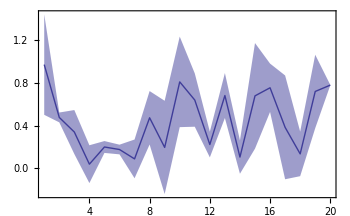
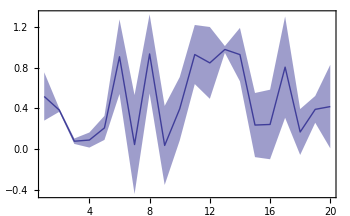
Show[Show[-Graphics-,Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Show[Sequence[Hold[Show[Sequence@@MapIndexed[errorListPlotBand[#1,Join[{PlotStyle→{ColorData[1][#2⟦1⟧],None,None},FillingStyle→«1»}]]&,{Hold[«1»],«1»}]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]],«1»,Show[-Graphics-,Show[«1»]]]

```mathematica
errorListPlotBand[RandomReal[{0.5,1},{20,2}],FrameLabel->{"x","y"}]
errorListPlotBand[Sequence@@RandomReal[{0,1},{3,20,2}],FrameLabel->{"x","y"}]
```

### Power spectra

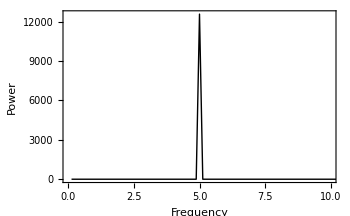

```mathematica
data=Table[Sin[5*p],{p,0,16Pi,.001}];
ListPlot[powerSpectrum[data,16Pi],Joined->True,FrameLabel->{"Frequency","Power"},PlotRange->{{0,10},All}]
```

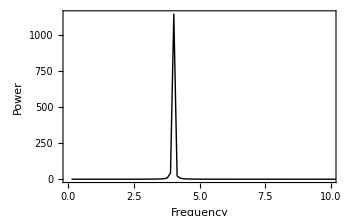

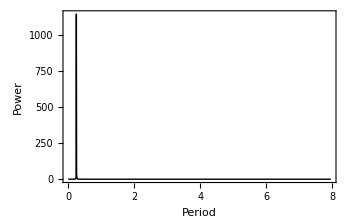

```mathematica
data=Table[Sin[4*p],{p,0,50,.01}];
ListPlot[powerSpectrum[data,50.],Joined->True,FrameLabel->{"Frequency","Power"},PlotRange->{{0,10},All}]
ListPlot[{1/#[[1]],#[[2]]}&/@powerSpectrum[data,50.],Joined->True,FrameLabel->{"Period","Power"},PlotRange->{All,All}]
```